```mathematica
S[z_]:=z^2/2+Log[z]-X z
```

```mathematica
S'[1]/.X->2
```

0

```mathematica
Series[S[1+w]/.X->2,{w,0,3}]
```

-3/2+w^3/3+O[w]^4

```mathematica
Clear[X]
```

```mathematica
z/.Solve[S'[z]==0,z]
```

```mathematica
zm:=1/2 (X-√(-4+X^2));zp:=1/2 (X+√(-4+X^2))
```

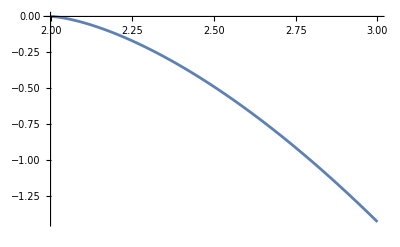

```mathematica
Plot[S[zp]-S[zm],{X,2,3}]
```

```mathematica
zcr:=1/4 (1+ⅈ √15)
```

```mathematica
X:=1/2
```

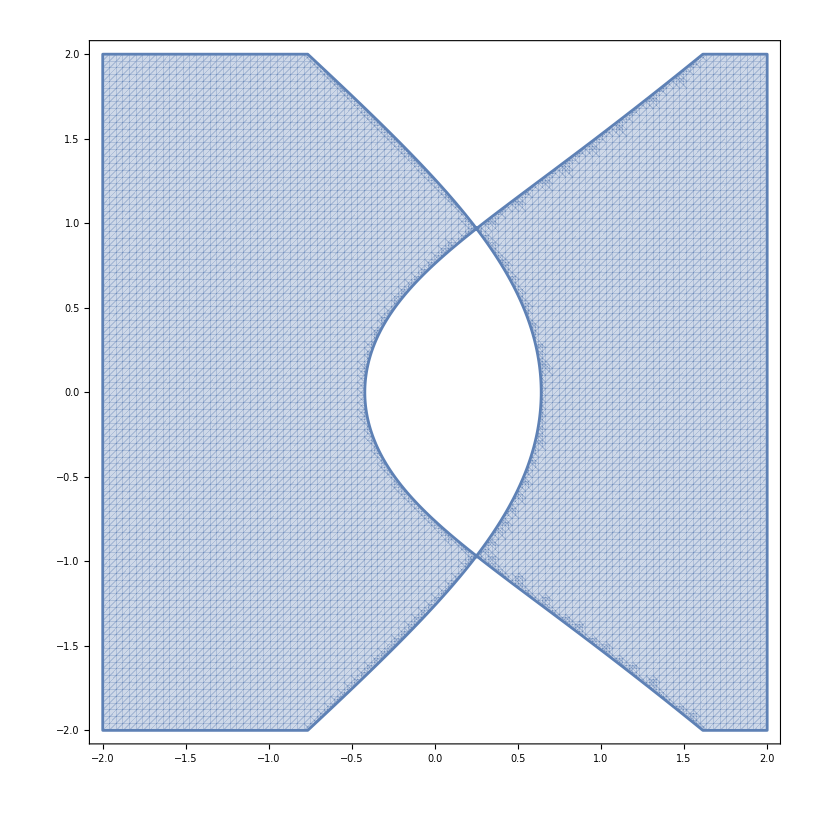

```mathematica
RegionPlot[Re[S[x+I y]]-Re[S[zcr]]>0,{x,-2,2},{y,-2,2},PlotPoints->100]
```

```mathematica
Plot3D[Re[S[x+I y]],{x,-2,2},{y,-2,2},PlotPoints->100,Exclusions->None,ViewVertical->{0,0,1},ViewPoint->{2,-3,1/2},ImageSize->600,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leo/Homepage/rmt25/rmt25-notes/pictures

```mathematica
Export["ReS_imaginary_3D.pdf",Plot3D[Re[S[x+I y]],{x,-2,2},{y,-2,2},PlotPoints->100,Exclusions->None,ViewVertical->{0,0,1},ViewPoint->{2,-3,1/2},ImageSize->600,AxesLabel->Automatic]]
```

ReS_imaginary_3D.pdf

```mathematica
Export["ReS_imaginary_region.pdf",RegionPlot[Re[S[x+I y]]-Re[S[zcr]]>0,{x,-2,2},{y,-2,2},PlotPoints->100]]
```

ReS_imaginary_region.pdf

```mathematica
-I/2/Pi Integrate[E^(z a),{z,-I,1,I}]//FullSimplify
```

Sin[a]/(a π)

```mathematica
Series[(s^2/2-t^2/2+t x-  s y+n Log[s/t])/.t->Sqrt[n](1+U/n^(1/3))/.s->Sqrt[n](1+V/n^(1/3))/.x->2Sqrt[n]+ξ/n^(1/6)/.y->2Sqrt[n]+η/n^(1/6),{n,Infinity,0}]//FullSimplify
```

(-η+ξ) n^(1/3)+1/3 (-U^3+V^3-3 V η+3 U ξ)+O[1/n]^(1/6)

```mathematica
1/3 (-U^3+V^3-3 V η+3 U ξ)//TeXForm
```

\frac{1}{3} \left(-U^3+3 \xi  U+V^3-3 \eta  V\right)

```mathematica
X:=2
```

```mathematica
S[1]
```

-3/2

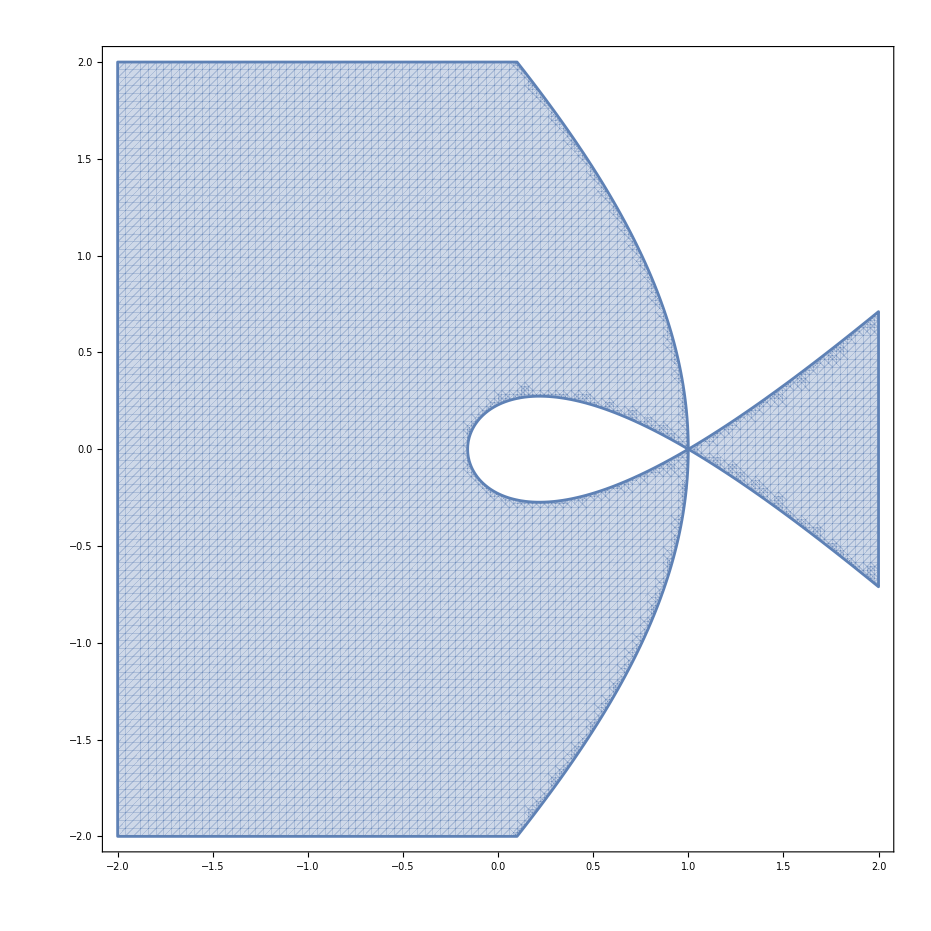

```mathematica
RegionPlot[Re[S[x+I y]]+3/2>0,{x,-2,2},{y,-2,2},PlotPoints->100]
```

```mathematica
Export["ReS_edge.pdf",RegionPlot[Re[S[x+I y]]+3/2>0,{x,-2,2},{y,-2,2},PlotPoints->100]]
```

ReS_edge.pdf